```mathematica
RK4[f_,t0_,T_,u0_,h_] := (
n = Floor[(T-t0)/h];
yArr = Table[0, {i,0,n}];
yArr[[1]] = u0;
tArr = Table[t0+i*h,{i,0,n}];

For[i=1,i≤n,i++,
k1 = h*f[tArr[[i]], yArr[[i]]];
k2 = h*f[tArr[[i]]+h/2,yArr[[i]]+k1/2];
k3 = h*f[tArr[[i]] + h/2, yArr[[i]] + k2/2];
k4 = h*f[tArr[[i]] +h, yArr[[i]] + k3];
yArr[[i+1]] = yArr[[i]]+1/6*(k1+2*k2+2*k3+k4);
];
Transpose[{tArr,yArr}]
)
```

```mathematica
F[t_,u_] := 10*u*(1-u);
```

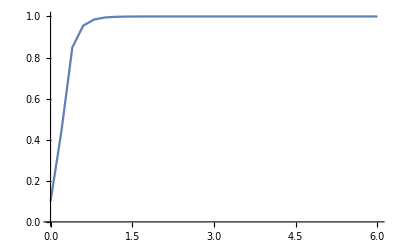

```mathematica
appr = ListLinePlot[RK4[F,0,6,0.1,0.2], PlotRange->All]
```

```mathematica
Clear[exact]
```

```mathematica
exact[t_] = DSolve[{u'[t] == 10*u[t]*(1-u[t]), u[0] == 0.1},u[t],t][[1,1,2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

ⅇ^(10 t)/(9.+ⅇ^(10 t))

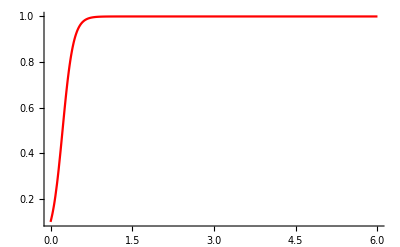

```mathematica
exactRes = Plot[exact[t],{t,0,6}, PlotRange->All, PlotStyle-> Red]
```

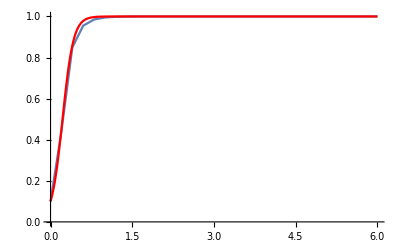

```mathematica
Show[appr,exactRes]
```

```mathematica
RK3[f_,t0_,T_,u0_,h_] := (
n = Floor[(T-t0)/h];
yArr = Table[0, {i,0,n}];
yArr[[1]] = u0;
tArr = Table[t0+i*h,{i,0,n}];

For[i=1,i≤n,i++,
k1 = h*f[tArr[[i]], yArr[[i]]];
k2 = h*f[tArr[[i]]+h/3,yArr[[i]]+k1/3];
k3 = h*f[tArr[[i]] + h*2/3, yArr[[i]] + k2*2/3];
yArr[[i+1]] = yArr[[i]]+1/4*k1+3/4*k3;
];
Transpose[{tArr,yArr}]
)
```

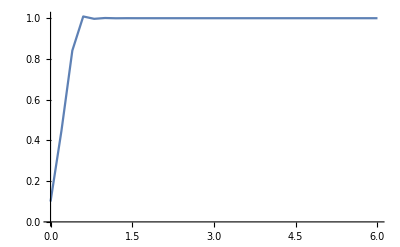

```mathematica
apprRK3 = ListLinePlot[RK3[F,0,6,0.1,0.2], PlotRange->All]
```

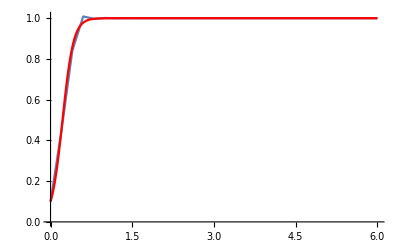

```mathematica
Show[apprRK3,exactRes]
```

```mathematica
apprSol = RK3[F,0,6,0.1,0.2]
```

{{0.,0.1},{0.2,0.446871},{0.4,0.841247},{0.6,1.0086},{0.8,0.996979},{1.,1.00099},{1.2,0.999669},{1.4,1.00011},{1.6,0.999963},{1.8,1.00001},{2.,0.999996},{2.2,1.},{2.4,1.},{2.6,1.},{2.8,1.},{3.,1.},{3.2,1.},{3.4,1.},{3.6,1.},{3.8,1.},{4.,1.},{4.2,1.},{4.4,1.},{4.6,1.},{4.8,1.},{5.,1.},{5.2,1.},{5.4,1.},{5.6,1.},{5.8,1.},{6.,1.}}

```mathematica
apprSol[[All,1]]
```

{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.}

```mathematica
apprSol[[All,2]]
```

{0.1,0.446871,0.841247,1.0086,0.996979,1.00099,0.999669,1.00011,0.999963,1.00001,0.999996,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
err = exact[apprSol[[All,1]]]-apprSol[[All,2]]
```

{-2.77556×10^-17,0.00398202,0.0172397,-0.030421,0.0000110094,-0.00139659,0.000276118,-0.000117727,0.0000357601,-0.0000123919,4.06671×10^-6,-1.36423×10^-6,4.5357×10^-7,-1.51349×10^-7,5.04281×10^-8,-1.68123×10^-8,5.6037×10^-9,-1.86795×10^-9,6.22644×10^-10,-2.07549×10^-10,6.9183×10^-11,-2.30609×10^-11,7.68696×10^-12,-2.56239×10^-12,8.54095×10^-13,-2.84661×10^-13,9.51461×10^-14,-3.15303×10^-14,1.05471×10^-14,-3.44169×10^-15,9.99201×10^-16}

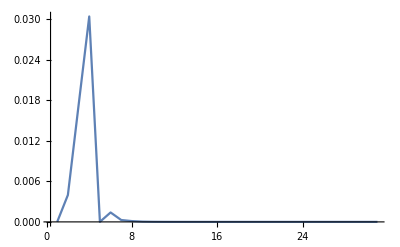

```mathematica
errPlot = ListLinePlot[Abs[err],PlotRange->All]
```